```mathematica
s[t_,ω_:1, σ_:2.4]:=1/π σ/(t^2+σ^2)Sin[ω t]
```

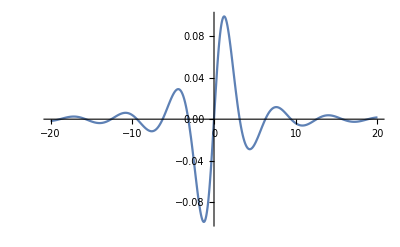

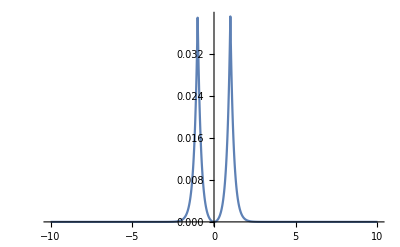

```mathematica
Plot[s[t],{t,-20, 20},PlotRange->Full]
Plot[Abs[S[ν]]^2,{ν,-10,10},PlotRange->Full]
FTSlow[l_]:=Module[{n=Length[l]},
1/(√Length[l])Table[Sum[l[[i]] ⅇ^(-2π ν),{i,1,n}],{ν,-n/2,n/2}]
]
```

```mathematica
S[ν_]=FourierTransform[s[t],t,ν]
```

0.763944 ((0.+0.261107 ⅈ) (Cosh[2.4 Abs[-1+ν]]-Sinh[2.4 Abs[-1+ν]])-(0.+0.261107 ⅈ) (Cosh[2.4 Abs[1+ν]]-Sinh[2.4 Abs[1+ν]]))

```mathematica
T=2000;
n=1024;
ts=Subdivide[-T/2,T/2,n-1];
δ=T/n
D1 =s[#]&/@ts;
```

125/64

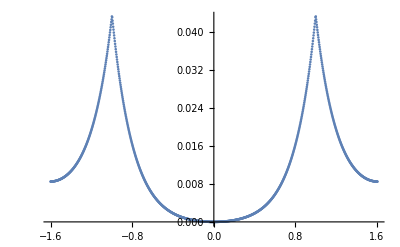

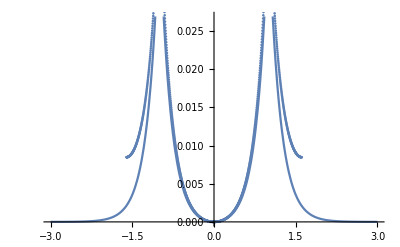

```mathematica
FTSlow[l_,δ_]:=Module[{n=Length[l]},
Table[{(z 2 π)/(n δ),1/(2π)Abs[δ Sum[l[[i]] ⅇ^(-ⅈ 2π  z i/n),{i,1,n}]]^2},{z,-n/2+1,n/2}]
]
S1=FTSlow[D1,δ];
ListPlot[S1]
```

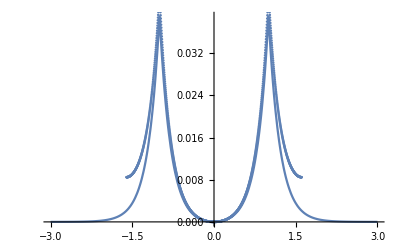

```mathematica
Show[{Plot[Abs[S[ν]]^2,{ν,-3,3},PlotRange->Full],ListPlot[S1]}]
```